## PN from FEWPackage Example

```mathematica
EllipE={e,p}|->EllipticE[4*e/(p-6.0+2*e)];
EllipK={e,p}|->EllipticK[4*e/(p-6.0+2*e)];
EllipPi1={e,p}|->EllipticPi[16*e/(12.0+8*e-4*e*e-8*p+p*p),4*e/(p-6.0+2*e)];
EllipPi2={e,p}|->EllipticPi[2*e*(p-4)/((1.0+e)*(p-6.0+2*e)),4*e/(p-6.0+2*e)];

Omegaphi={e,p}|->(2*Power[p,1.5])/(Sqrt[-4*Power[e,2]+Power[-2+p,2]]*(8+((-2*EllipPi2[e,p]*(6+2*e-p)*(3+Power[e,2]-p)*Power[p,2])/((-1+e)*Power[1+e,2])-(EllipE[e,p]*(-4+p)*Power[p,2]*(-6+2*e+p))/(-1+Power[e,2])+(EllipK[e,p]*Power[p,2]*(28+4*Power[e,2]-12*p+Power[p,2]))/(-1+Power[e,2])+(4*(-4+p)*p*(2*(1+e)*EllipK[e,p]+EllipPi2[e,p]*(-6-2*e+p)))/(1+e)+2*Power[-4+p,2]*(EllipK[e,p]*(-4+p)+(EllipPi1[e,p]*p*(-6-2*e+p))/(2+2*e-p)))/(EllipK[e,p]*Power[-4+p,2])));

yPN={e,p}|->Power[Omegaphi[e,p],2./3.];
EdotPN={e,p}|->-(96+292*Power[e,2]+37*Power[e,4])/(15.*Power[1-Power[e,2],3.5])*Power[yPN[e,p],5];
```

## Analytic

```mathematica
v = Sqrt[1/p];Y=0;
dEdtN={e,p,q}|->Evaluate[-32/5*v^6/p^2*(-e^2+1)^(3/2)];
dEdt8corr={e,p,q}|->Evaluate[1+73/24*e^2+37/96*e^4+(809/128*e^4+8609/5376*e^6-9181/672*e^2-1247/336)*v^2+((10007/9216*Pi-491/192*Y*q)*e^6-237857/88473600*Pi*e^10+(1375/48*Pi-823/24*Y*q)*e^2+(3935/192*Pi-949/32*Y*q)*e^4+2321/221184*Pi*e^8-73/12*Y*q+4*Pi)*v^3+(-44711/9072-329/96*q^2+527/96*Y^2*q^2+(-172157/2592-4379/192*q^2+6533/192*Y^2*q^2)*e^2+(-2764345/24192-3823/256*q^2+6753/256*Y^2*q^2)*e^4+(3743/2304+1/4608*(-3267+8565*Y^2)*q^2)*e^6+198377/64512*e^8-1645/2048*e^10)*v^4+((15670391/387072*Pi-49685/448*Y*q)*e^6+(9561889/77414400*Pi+329/256*Y*q)*e^10+(-44531/336*Pi+1759/56*Y*q)*e^2+(-4311389/43008*Pi-111203/1344*Y*q)*e^4+(32271047/7077888*Pi-144139/14336*Y*q)*e^8+3749/336*Y*q-8191/672*Pi)*v^5+(Log[v]*(-1712/105-14552/63*e^2-553297/1260*e^4-187357/1260*e^6-10593/2240*e^8)+16/3*Pi^2-1712/105*EulerGamma-3424/105*Log[2]+6643739519/69854400+135/8*q^2-169/6*Pi*Y*q+73/21*Y^2*q^2+(680/9*Pi^2-14552/63*EulerGamma-13696/315*Log[2]-234009/560*Log[3]+43072561991/27941760+205747/1344*q^2-4339/16*Pi*Y*q+13697/192*Y^2*q^2)*e^2+(5171/36*Pi^2-553297/1260*EulerGamma-12295049/1260*Log[2]+2106081/448*Log[3]+919773569303/279417600+208571/1792*q^2-42271/96*Pi*Y*q+471711/1792*Y^2*q^2)*e^4+(1751/36*Pi^2-187357/1260*EulerGamma+24908851/252*Log[2]-864819261/35840*Log[3]-5224609375/193536*Log[5]+308822406727/186278400+3253/10752*q^2-4867907/27648*Pi*Y*q+289063/1536*Y^2*q^2)*e^6+(99/64*Pi^2-10593/2240*EulerGamma-13091486273/20160*Log[2]-2480573403/40960*Log[3]+496337890625/1548288*Log[5]+2087886792107/2980454400-12577/86016*q^2-134279/16384*Pi*Y*q+1110551/86016*Y^2*q^2)*e^8+(369490499473/851558400-262029833984375/148635648*Log[5]+346080010951719/229376000*Log[3]-507989081563901/884736000*Log[7]+536743821479/162000*Log[2]+329/768*q^2-2289029/17694720*Pi*Y*q-1645/1024*Y^2*q^2)*e^10)*v^6+(-16285/504*Pi-809/48*Pi*q^2+83819/1296*Y*q+1049/48*Y*q^3+1199/48*Pi*Y^2*q^2-551/16*Y^3*q^3+(-22798583/48384*Pi+11/32*(-605+812*Y^2)*Pi*q^2+12203083/18144*Y*q-1/96*(-24299+37293*Y^2)*Y*q^3)*e^2+(-65448785/48384*Pi-520049/1536*Pi*q^2+3918011/2268*Y*q+58613/128*Y*q^3+242169/512*Pi*Y^2*q^2-86695/128*Y^3*q^3)*e^4+(-41758768871/41803776*Pi-5314081/55296*Pi*q^2+1325729/1728*Y*q+37863/256*Y*q^3+4618853/27648*Pi*Y^2*q^2-63441/256*Y^3*q^3)*e^6+(-306245599/7962624*Pi-3081197/1179648*Pi*q^2-2591615/14336*Y*q+14033/3072*Y*q^3+2527249/393216*Pi*Y^2*q^2-331/32*Y^3*q^3)*e^8+(183849241019/107017666560*Pi+378811/35389440*Pi*q^2-79873/258048*Y*q-329/512*Y*q^3+57613/921600*Pi*Y^2*q^2+329/256*Y^3*q^3)*e^10)*v^7+(Log[v]*(232597/4410+831307/588*e^2+25695073/5880*e^4+14109647/7056*e^6-5771555/37632*e^8-2270637/125440*e^10)+39931/294*Log[2]-47385/1568*Log[3]-1369/126*Pi^2+232597/4410*EulerGamma-323105549467/3178375200+1/25427001600*(-524253930200+176451675400*Y^2)*q^2+3389/96*Pi*Y*q+1/25427001600*(354355726725-760624915050*Y^2+433285377525*Y^4)*q^4+(-2373293/1260*Log[2]+55105839/15680*Log[3]-83045/252*Pi^2+831307/588*EulerGamma-13084171033763/3178375200+1/50854003200*(-29346287170200+64166474972600*Y^2)*q^2+57405/224*Pi*Y*q+1/50854003200*(9239636030625-21421917767250*Y^2+13069048417425*Y^4)*q^4)*e^2+(2273961523/17640*Log[2]-3074548023/71680*Log[3]-15869140625/903168*Log[5]-56023/56*Pi^2+25695073/5880*EulerGamma-454079900391707/25427001600+1/203416012800*(-261728304637800+621690103634600*Y^2)*q^2-15198859/43008*Pi*Y*q+1/203416012800*(63296249541525-162222614804250*Y^2+104646381164325*Y^4)*q^4)*e^4+(-503388564173/317520*Log[2]+107130980133/1003520*Log[3]+10089048828125/16257024*Log[5]-327895/1008*Pi^2+14109647/7056*EulerGamma-12759433101997/847566720+1/81366405120*(-59943440156600+185814906677400*Y^2)*q^2-59177891/64512*Pi*Y*q+1/81366405120*(7543403402535-21808116840510*Y^2+15329681021655*Y^4)*q^4)*e^6+(68231217040939/5080320*Log[2]+467815486759011/128450560*Log[3]-14588154185546875/2080899072*Log[5]-44084499735185/42467328*Log[7]+1721345/16128*Pi^2-5771555/37632*EulerGamma-2378391544181/391184640+1/801146142720*(-33053844700800+604446021970560*Y^2)*q^2-25122496349/49545216*Pi*Y*q+1/801146142720*(1993183536960-7023655013760*Y^2+5557136397120*Y^4)*q^4)*e^8+(-8682554270274823/84672000*Log[2]-310548285495073989/6422528000*Log[3]+2214348251953125/51380224*Log[5]+99735805288105217/3538944000*Log[7]+24933/3584*Pi^2-2270637/125440*EulerGamma-352368216244361/90407116800+1/173581664256000*(3835398831264000-3569717607456000*Y^2)*q^2-3412842619/137625600*Pi*Y*q+1/173581664256000*(-3485618136000+62741126448000*Y^2-87140453400000*Y^4)*q^4)*e^10)*v^8+(-13696/105*Pi*Log[2]-6848/105*EulerGamma*Pi+265978667519/745113600*Pi+216403/2688*Pi*q^2-385/9*Pi^2*Y*q+95723/315*Log[2]*Y*q+1369/9*EulerGamma*Y*q-343985009/498960*Y*q-1237/336*Y*q^3+96937/2688*Pi*Y^2*q^2-8075/112*Y^3*q^3+(1/447068160*(-363366001152*Pi+141852598272*Y*q)*Log[2]+1/447068160*(-1120906854144*Pi+2110284658944*Y*q)*Log[3]+1/447068160*(-742411676160*EulerGamma+4834416801761)*Pi+1/447068160*(715708722960*Pi+49634046000*Pi*Y^2)*q^2+1/447068160*(-290470118400*Pi^2+1130841169920*EulerGamma-6452588971968)*Y*q+1/447068160*(329581707840*Y-1217459073600*Y^3)*q^3)*e^2+(1/71530905600*(-5598260123258880*Pi+9025243008122880*Y*q)*Log[2]+1/71530905600*(2286649982453760*Pi-4162999169387520*Y*q)*Log[3]+1/71530905600*(-461122123714560*EulerGamma+3439243750356319)*Pi+1/71530905600*(286911926393400*Pi+34098821202600*Pi*Y^2)*q^2-21443/12*(Pi^2-3179761/750505*EulerGamma+361951335499/15130180800)*Y*q+1/71530905600*(152341934976000*Y-466229554560000*Y^3)*q^3)*e^4+(1/8047226880*(7084738842671952*Pi-10340888111059968*Y*q)*Log[2]+1/8047226880*(-1513119168076824*Pi+2526730618231512*Y*q)*Log[3]+1/8047226880*(-2172392578125000*Pi+2900367421875000*Y*q)*Log[5]+1/8047226880*(-47209634120880*EulerGamma+435704767921187)*Pi+1/8047226880*(15781168917360*Pi+12124009456020*Pi*Y^2)*q^2+1/8047226880*(-12911887296000*Pi^2+54902365056000*EulerGamma-362102856883560)*Y*q+1/8047226880*(13827402056160*Y-37279194654240*Y^3)*q^3)*e^6+(1/21974294200320*(-151836933639344701440*Pi+186928083596694257664*Y*q)*Log[2]+1/21974294200320*(-20834268796210028544*Pi+19055185075880110080*Y*q)*Log[3]+1/21974294200320*(79341570000000000000*Pi-93186550380000000000*Y*q)*Log[5]+1/21974294200320*(-26076813703987200*EulerGamma+483141287981432359)*Pi+1/21974294200320*(3249360060518880*Pi+19165555054023840*Pi*Y^2)*q^2-487355/1152*(Pi^2-13553357/3411485*EulerGamma+1449035920823/25217697120)*Y*q+1/21974294200320*(5690766374092800*Y-25682502841712640*Y^3)*q^3)*e^8+(1/2322432000*(97515544148275847*Pi-97793656374620672*Y*q)*Log[2]+1/114688000*(2380413947183397*Pi-2280624020922231*Y*q)*Log[3]+361328125/74317824*(-4635775*Pi+4588691*Y*q)*Log[5]+688360827060361/88473600*(-1798349/1740635*Pi+Y*q)*Log[7]+1/2746786775040000*(-70490400688942080*EulerGamma+27109967180184051997)*Pi+1/4954521600*Pi*(10360437581+178739355031*Y^2)*q^2+1/198696960*(-2577627360*Pi^2+9521753472*EulerGamma-2546262906169)*Y*q+1/28672*(-1227693+1246121*Y^2)*Y*q^3)*e^10+(1369/9*Y*q-6848/105*Pi+1/252*(637424*Y*q-418477*Pi)*e^2+1/5040*(38157132*Y*q-32490229*Pi)*e^4+(1719275/252*Y*q-283848209/48384*Pi)*e^6+1/1161216*(1951683408*Y*q-1378010735*Pi)*e^8+(107343/2240*Y*q-59600244089/2322432000*Pi)*e^10)*Log[v])*v^9+(-287509/2520*EulerGamma*Y^2*q^2-2541/16*Pi*Y^3*q^3-115025/504*Log[2]*Y^2*q^2+1049395/3024*Pi*Y*q+2687/72*Pi^2*Y^2*q^2+4873/48*Pi*Y*q^3+916628467/7858620*EulerGamma+(1/2319918942781440*(-344965551717851861724928+(17904109471863196982400-18601020087195575981952*Y^2)*q^2)*Log[2]+1/2319918942781440*(-154508844523957183692432+(1868720146933658317299-1990085883851087115093*Y^2)*q^2)*Log[3]+1/2319918942781440*(147734675246594373437500+(-8965011593203681640625+9340424140615927734375*Y^2)*q^2)*Log[5]+179353293697576705/4729798656*Log[7]-3403135585/870912*Pi^2+1799597206189/201180672*EulerGamma-21626538680259344683/289989867847680+1/2319918942781440*(-554740296372662400*Pi^2+1695920334624996480*EulerGamma-47804578393625693640+(966488149618992000*Pi^2-2954692343120918400*EulerGamma+60448980324352740120)*Y^2)*q^2+3911945775407/668860416*Pi*Y*q+1/2319918942781440*(1831256185115632275*Pi*Y-3147238414078844085*Pi*Y^3)*q^3+1/2319918942781440*(105454992775712580-2372461583102530920*Y^2+3357855963381219300*Y^4)*q^4)*e^8+(1/1855935154225152000*(3334181456997689578060132352+(-83958270832493829695379456+80504890373325282624055296*Y^2)*q^2)*Log[2]+1/1855935154225152000*(1067840387446770012584482974+(-38727865718486169464951712+37914541706425156347006432*Y^2)*q^2)*Log[3]+1/1855935154225152000*(-772152507683425188632812500+(44653595692643437500000000-42789280255440468750000000*Y^2)*q^2)*Log[5]+1/1855935154225152000*(-1151872682245551035245074599+(14846374863236423260786032-14701688061484156542810000*Y^2)*q^2)*Log[7]-5696423/64512*Pi^2+41387540881/74511360*EulerGamma-398657589092616827/16110548213760+1/1855935154225152000*(-8006439007607040000*Pi^2+24476827823255808000*EulerGamma-15270670558956583330560+(19636845144973056000*Pi^2-60032640871774771200*EulerGamma+22036717896941501994240)*Y^2)*q^2+200289353539571/535088332800*Pi*Y*q+1/1855935154225152000*(-5891899886688816000+61146559057487904000*Y^2-71174887149366000000*Y^4)*q^4-577328143/17694720*(-73879067/164950898+Y^2)*Pi*Y*q^3)*e^10+(1/60414555801600*(-47915984063338110720+(5288110552792267200-6378925984613582400*Y^2)*q^2)*Log[2]+1/60414555801600*(3962413191335548950+(-2373877640280526380+2883523687346402100*Y^2)*q^2)*Log[3]+120783447265625/402361344*Log[5]-43066675/9072*Pi^2+4126196653/5239080*EulerGamma-1261125137775896021/15103638950400+1/60414555801600*(-109887154501924800*Pi^2+335940729477312960*EulerGamma-2330160763548852234+(132334937891956800*Pi^2-404566810126839360*EulerGamma+2552261058353740734)*Y^2)*q^2+3525482221/193536*Pi*Y*q+1/60414555801600*(282850291184561100*Pi*Y-409311880144467300*Pi*Y^3)*q^3+1/60414555801600*(-195866095596546375-59208166687720050*Y^2+438252072025192425*Y^4)*q^4)*e^4+(1/45310916851200*(1356784527238620480+(21941299040300640-20146285492613280*Y^2)*q^2)*Log[2]+1/45310916851200*(-478119993043042350+(132539529267905760-170407966201593120*Y^2)*q^2)*Log[3]-383544921875/100590336*Log[5]-16023095/13608*Pi^2+2849613677/3143448*EulerGamma-107175721853269621/5663864606400+1/45310916851200*(-25341703544757600*Pi^2+77473207979687520*EulerGamma-499904270375337828+(31279321607133600*Pi^2-95625354627522720*EulerGamma+680799913794108108)*Y^2)*q^2+85633087/16128*Pi*Y*q+1/45310916851200*(70160650823062800*Pi*Y-106317346504168800*Pi*Y^3)*q^3+1/45310916851200*(-68613914297503575-7934020767322650*Y^2+140901641273217825*Y^4)*q^4)*e^2+(1/26362715258880*(318068362925621048832+(-26578488801577160448+29791690403510939904*Y^2)*q^2)*Log[2]+1/26362715258880*(78820169617231176771+(6266021407713731664-7097864739023730672*Y^2)*q^2)*Log[3]+1/26362715258880*(-161814595842508984375+(7572230603437500000-8483175638437500000*Y^2)*q^2)*Log[5]-1065488447445779/1182449664*Log[7]-443246159/54432*Pi^2+54196501451/5715360*EulerGamma-20551635274449925/164766970368+1/26362715258880*(-36831138952608000*Pi^2+112598053369401600*EulerGamma-1097117224009344720+(49887548296185600*Pi^2-152513361934053120*EulerGamma+1189957613746552560)*Y^2)*q^2+260806848791/13934592*Pi*Y*q+1/26362715258880*(101571353588544840*Pi*Y-149144632980623280*Pi*Y^3)*q^3+1/26362715258880*(-29851071387277140-69590361567406680*Y^2+144601161399234540*Y^4)*q^4)*e^6+3712887509/12700800*Y^2*q^2+410131/2520*Log[2]*q^2+204691/2520*EulerGamma*q^2-1913/72*Pi^2*q^2+334235/2688*Y^4*q^4+9321/448*Y^2*q^4-62206109341/139708800*q^2-424223/6804*Pi^2-83217611/1122660*Log[2]+47385/196*Log[3]-256201/2688*q^4-2500861660823683/2831932303200+Log[v]*(916628467/7858620+1/4023613440*(-459057570048*Y^2+326824388352)*q^2+1/4023613440*(3647505506560+(-8491539982464*Y^2+6879627748224)*q^2)*e^2+1/4023613440*(3168919029504+(-26944176498624*Y^2+22373674956864)*q^2)*e^4+1/4023613440*(38154337021504+(-23277375142560*Y^2+17185295080800)*q^2)*e^6+1/4023613440*(35991944123780+(-5124549657150*Y^2+2941364771730)*q^2)*e^8+1/4023613440*(2234927207574+(-130149019539*Y^2+53065050885)*q^2)*e^10))*v^10];
dEdtAn= {e,p,q}|->dEdtN[e,p,q]*dEdt8corr[e,p,q];
```

## Numerical

```mathematica
numdatraw = Import["/home/shaunf/Documents/Computer/Code/projects/Massive_Vector_Field_Dynamical_Friction/ProcaAroundKerr/GWGenerator/numerical_flux/dIdt_q0.90inc0.dat", "Table"];
tags = {"q", "p", "e", "inc", "E", "Lz", "C", "Einf", "Linf", "Cinf", "Eh", "Lh", "Ch", "pinf", "einf", "incinf","ph", "eh", "inch", "lmax", "DeltaEinf", "DeltaEh"};
numdat = Table[Association@@Thread[tags->numdatraw[[i]]],{i,1,Length[numdatraw]}];
dEdtNum = {e,p,q}|->(nearestval = Nearest[Evaluate[List@@@numdat[[All, {"e", "p", "q"}]]],{e,p,q}]//First;
inx = Position[Evaluate[List@@@numdat[[All, {"e", "p", "q"}]]], nearestval][[1,1]];
numdat[[inx, "Einf"]]
);
InterpDat = Thread[{List@@@numdat[[1;;255, {"e", "p", "q"}]], List@@@numdat[[1;;255, "Einf"]]}];
dEdtNumInterp = Interpolation[InterpDat, InterpolationOrder->3];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0,3,0}.

```mathematica
dEdtNumInterp[0.005,30,0.9]
dEdtNum[0.005,30,0.9]
```

-2.40409×10^-7

-2.40409×10^-7

## Comparison

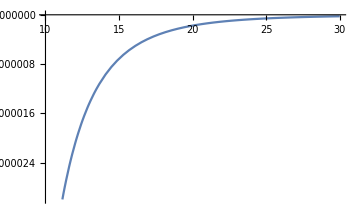
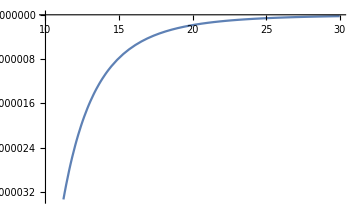
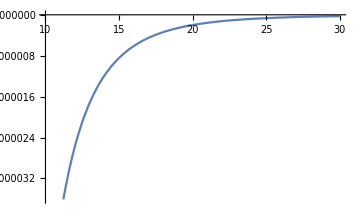

```mathematica
With[{e = 0.005, p = 20, spin = 0.9},
Row[{
Plot[dEdtNumInterp[e,P,spin], {P, 10, 30}, ImageSize->Medium],
Plot[dEdtAn[e,P,spin], {P, 10, 30}, ImageSize->Medium],
Plot[EdotPN[e,P,spin], {P, 10, 30}, ImageSize->Medium]
}]
]
```

```mathematica
dEdtAn[0,20,0.9]
```

-1.85855×10^-6